```mathematica
$Assumptions = K ∈ Reals && D ∈ Reals  && O ∈ Reals && K ≥ 0 && D ≥ 0 && O ≥ 0 && t ≥ 0 && tsep ≥ 0
```

K∈ℝ&&D∈ℝ&&O∈ℝ&&K≥0&&D≥0&&O≥0&&t≥0&&tsep≥0

```mathematica
M = {{0, O/2},{O/2, D}}
```

{{0,O/2},{O/2,D}}

```mathematica
Diag = DiagonalMatrix[Eigenvalues[M]]
```

{{1/2 (D-√(D^2+O^2)),0},{0,1/2 (D+√(D^2+O^2))}}

```mathematica
S = Simplify[Transpose[Normalize/@Eigenvectors[M]]]
```

{{-(D+√(D^2+O^2))/(O √(1+((D+√(D^2+O^2))^2)/O^2)),(-D+√(D^2+O^2))/(√2 √(D^2+O^2-D √(D^2+O^2)))},{1/(√(1+((D+√(D^2+O^2))^2)/O^2)),1/(√(1+((D-√(D^2+O^2))^2)/O^2))}}

```mathematica
Simplify[Conjugate[D]]
```

D

```mathematica
Sdag = Simplify[ConjugateTranspose[S]]
```

{{-(D+√(D^2+O^2))/(O √(1+((D+√(D^2+O^2))^2)/O^2)),1/(√(1+((D+√(D^2+O^2))^2)/O^2))},{(-D+√(D^2+O^2))/(√2 √(D^2+O^2-D √(D^2+O^2))),1/(√(1+((D-√(D^2+O^2))^2)/O^2))}}

```mathematica
Diag
```

{{1/2 (D-√(D^2+O^2)),0},{0,1/2 (D+√(D^2+O^2))}}

```mathematica
Simplify[Sdag.Diag.S]
```

{{0,O/2},{O/2,D}}

```mathematica
F = {{0,0},{0,K}}
```

{{0,0},{0,K}}

```mathematica
FM = Simplify[S.F.Sdag]
```

{{(K (D-√(D^2+O^2))^2)/(2 (D^2+O^2-D √(D^2+O^2))),(K O (-D+√(D^2+O^2)))/(2 (D^2+O^2-D √(D^2+O^2)))},{(K O (-D+√(D^2+O^2)))/(2 (D^2+O^2-D √(D^2+O^2))),K/(1+((D-√(D^2+O^2))^2)/O^2)}}

```mathematica
expFM = Simplify[MatrixExp[-I*FM]]
```

{{(ⅇ^(-ⅈ K) (-4 D^4-D^2 (5+ⅇ^(ⅈ K)) O^2-(1+ⅇ^(ⅈ K)) O^4+4 D^3 √(D^2+O^2)+D (3+ⅇ^(ⅈ K)) O^2 √(D^2+O^2)))/(2 (D^2+O^2) (-2 D^2-O^2+2 D √(D^2+O^2))),((-1+ⅇ^(-ⅈ K)) O (-D+√(D^2+O^2)) (-D^2-O^2+D √(D^2+O^2)))/(2 (D^2+O^2) (-2 D^2-O^2+2 D √(D^2+O^2)))},{((-1+ⅇ^(-ⅈ K)) O (-D+√(D^2+O^2)) (-D^2-O^2+D √(D^2+O^2)))/(2 (D^2+O^2) (-2 D^2-O^2+2 D √(D^2+O^2))),(-4 D^4+D^2 (-5-ⅇ^(-ⅈ K)) O^2+(-1-ⅇ^(-ⅈ K)) O^4+4 D^3 √(D^2+O^2)+D ⅇ^(-ⅈ K) (1+3 ⅇ^(ⅈ K)) O^2 √(D^2+O^2))/(2 (D^2+O^2) (-2 D^2-O^2+2 D √(D^2+O^2)))}}

```mathematica
expDiag[t_]:= Simplify[MatrixExp[-I*t*Diag]]
```

```mathematica
expDiag[t]
```

{{ⅇ^(1/2 ⅈ (-D+√(D^2+O^2)) t),0},{0,ⅇ^(-1/2 ⅈ (D+√(D^2+O^2)) t)}}

```mathematica
Utot[tsep_]:=FullSimplify[expFM.expDiag[tsep].expFM]
```

```mathematica
Rho0 = {{1,0},{0,0}}
```

{{1,0},{0,0}}

```mathematica
Rho0M = FullSimplify[S.Rho0.Sdag]
```

{{1/2 (1+D/(√(D^2+O^2))),-O/(2 √(D^2+O^2))},{-O/(2 √(D^2+O^2)),1/2-D/(2 √(D^2+O^2))}}

```mathematica
RhoM[tsep_]:= FullSimplify[ConjugateTranspose[Utot[tsep]].Rho0M.Utot[t,tsep]]
```

```mathematica
RhoM[tsep]
```

{{(ⅇ^(-1/2 ⅈ (-D+√(D^2+O^2)) tsep) (2 D^3+2 D O^2+2 D^2 √(D^2+O^2)-(-1-ⅇ^(ⅈ K)+ⅇ^(ⅈ √(D^2+O^2) tsep) (-1+ⅇ^(ⅈ K))) O^2 √(D^2+O^2)))/(4 (D^2+O^2)^(3/2)),-(ⅇ^(1/2 ⅈ (K+D tsep)) O ((D^2+O^2-D √(D^2+O^2)) Cos[1/2 (K-√(D^2+O^2) tsep)]+D √(D^2+O^2) Cos[1/2 (K+√(D^2+O^2) tsep)]-ⅈ (D^2+O^2) Sin[1/2 (K+√(D^2+O^2) tsep)]))/(2 (D^2+O^2)^(3/2))},{-(ⅇ^((ⅈ D tsep)/2) O ((D^2+O^2) Cos[1/2 √(D^2+O^2) tsep]+ⅈ (D^2 ⅇ^(ⅈ K)+ⅇ^(ⅈ K) O^2+D (-1+ⅇ^(ⅈ K)) √(D^2+O^2)) Sin[1/2 √(D^2+O^2) tsep]))/(2 (D^2+O^2)^(3/2)),(ⅇ^(-1/2 ⅈ (-D+√(D^2+O^2)) tsep) (-2 D^3 ⅇ^(ⅈ √(D^2+O^2) tsep)-2 D ⅇ^(ⅈ √(D^2+O^2) tsep) O^2+2 D^2 ⅇ^(ⅈ √(D^2+O^2) tsep) √(D^2+O^2)+(1-ⅇ^(ⅈ K)+ⅇ^(ⅈ √(D^2+O^2) tsep) (1+ⅇ^(ⅈ K))) O^2 √(D^2+O^2)))/(4 (D^2+O^2)^(3/2))}}.Utot[t,tsep]

```mathematica
$Assumptions = a≥0&& a≤1 && K ∈ Reals && D ∈ Reals  && O ∈ Reals && K ≥ 0 && D ≥ 0 && O ≥ 0 && t ≥ 0 && tsep ≥ 0
```

a≥0&&a≤1&&K∈ℝ&&D∈ℝ&&O∈ℝ&&K≥0&&D≥0&&O≥0&&t≥0&&tsep≥0

```mathematica
H = {{a,b},{Conjugate[b],1-a}}
```

{{a,b},{Conjugate[b],1-a}}

```mathematica
H = {{1-a,0},{0,a}}
```

{{1-a,0},{0,a}}

```mathematica
{{1-a,0},{0a}}
```

{{1-a,0},{0}}

```mathematica
FullSimplify[Sdag.H.S]
```

{{(D-2 a D+√(D^2+O^2))/(2 √(D^2+O^2)),((-1+2 a) O)/(2 √(D^2+O^2))},{((-1+2 a) O)/(2 √(D^2+O^2)),1/2 (1+((-1+2 a) D)/(√(D^2+O^2)))}}

```mathematica
PopupationAverage[tsep_] := FullSimplify[(Sdag.RhoM[tsep].S)[[2,2]]]
```

```mathematica
PopupationAverage[tsep_]
```

$Aborted

```mathematica
FullSimplify[1/2 (1+((-1+2 (-D^3+D^2 √(D^2+O^2)+O^2 √(D^2+O^2)+O^2 (-D Cos[K]+D (-1+Cos[K]) Cos[√(D^2+O^2) tsep]-√(D^2+O^2) Sin[K] Sin[√(D^2+O^2) tsep]))/(2 (D^2+O^2)^(3/2))) D)/(√(D^2+O^2))) ]
```

(O^2 (2 D^2+O^2-D (D (Cos[K]-(-1+Cos[K]) Cos[√(D^2+O^2) tsep])+√(D^2+O^2) Sin[K] Sin[√(D^2+O^2) tsep])))/(2 (D^2+O^2)^2)

```mathematica
$Assumptions = D == 250 && K ==π && O == 100
```

D==250&&K==π&&O==100

```mathematica
Ramsey[tsep_]:=FullSimplify[ (O^2 (2 D^2+O^2-D (D (Cos[K]-(-1+Cos[K]) Cos[√(D^2+O^2) tsep])+√(D^2+O^2) Sin[K] Sin[√(D^2+O^2) tsep])))/(2 (D^2+O^2)^2)]
```

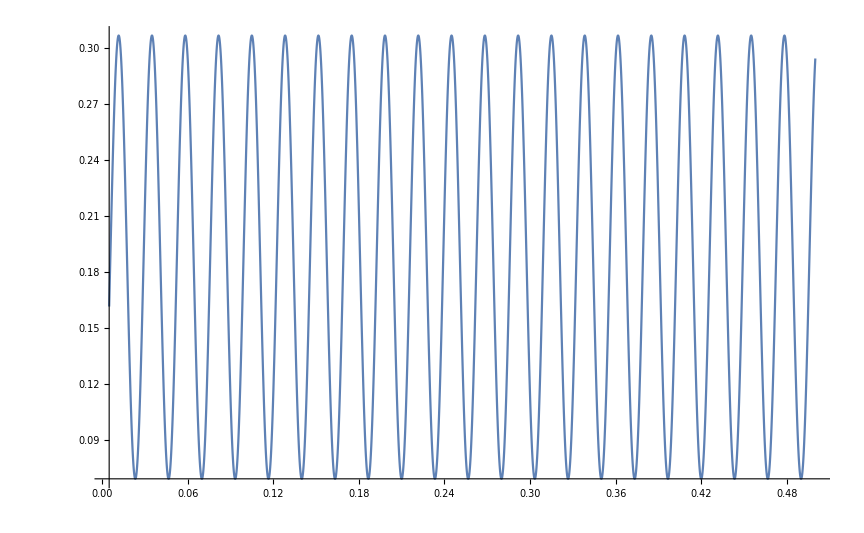

```mathematica
Plot[Ramsey[t],{t, 0.005, 0.500}]
```

```mathematica
FullSimplify[MatrixExp[-I π/4.PauliMatrix[2]]] //MatrixForm
```

(0.707107+0. ⅈ | -0.707107+0. ⅈ
0.707107+0. ⅈ | 0.707107+0. ⅈ)

```mathematica
PauliMatrix[2]
```

{{0,-ⅈ},{ⅈ,0}}

```mathematica
Rh0T= FullSimplify[Sdag.Rho0.S]
```

{{1/2 (1+D/(√(D^2+O^2))),-O/(2 √(D^2+O^2))},{-O/(2 √(D^2+O^2)),1/2-D/(2 √(D^2+O^2))}}

```mathematica
Rh0T //MatrixForm
```

(1/2 (1+D/(√(D^2+O^2))) | -O/(2 √(D^2+O^2))
-O/(2 √(D^2+O^2)) | 1/2-D/(2 √(D^2+O^2)))

```mathematica
FullSimplify[ArcTan[(O/(D+√(D^2+O^2)))^-1]]
```

ArcTan[(D+√(D^2+O^2))/O]

```mathematica
FullSimplify[N[O/(D+√(D^2+O^2))==Tan[π/8],5]]
```

O/(D+√(D^2+O^2))==0.41421

```mathematica
2Tan[π/8]/(1-Tan[π/8]^2)
```

(2 Tan[π/8])/(1-Tan[π/8]^2)

```mathematica
RootReduce[(2 Tan[π/8])/(1-Tan[π/8]^2)]
```

1